```mathematica
(*блок ввода*)
(*холестерик*)
{ϵ1 = 1,ϵ2 = 1.2,q =10, L =1};
(*траектория, заряд*)
{β3=1,Z =1,e=1};

(*где из файла ko := Subscript[k, 0], k0:= \overline Subscript[{k}, 0],kp:= k_\perp,k3:= Sqrt[k0^2-kp^2],θ:=\overline{θ}, ϵ1:= ϵ_\parallel, ϵ2:=ϵ_\perp *)
```

```mathematica
(*иницализация*)
long ={k0= √ϵ2 ko,k3 =  √(ϵ2 ko^2-kp^2),θ =  q z - ϕ, δϵ =(ϵ1 - ϵ2)/ϵ2, np = kp/ko,n3= (√(ϵ2 ko^2-kp^2))/ko,n32 = (2/π EllipticE[(-kp^2 δϵ)/((1+δϵ)k3^2)] √(1+δϵ)k3)/ko,p3= 2/π EllipticE[(-kp^2 δϵ)/((1+δϵ)k3^2)] √(1+δϵ)k3, χ1 = ϵ1-1, χ2 = ϵ2-1};
S[θ_]:= q^-1 √((1+δϵ)k3^2)EllipticE[θ,(-kp^2 δϵ)/((1+δϵ)k3^2)];
```

```mathematica
(*инициализация коэффициентов входящих в формулу для ВКБ - параксиального илзучения, см vrch*)

JJ[n_]:= BesselJ[n, (kp np δϵ)/(8q ϵ1^(1/2))];
x[n_]:= ko(1-n3 β3);
xx[n_]:= ko(1+n3 β3);
y[n_]:=ko(1-n32 β3);
yy[n_]:=ko(1+n32 β3);
d[n_]:= ϵ1^(-1/4)ϵ2^(-1/2)BesselJ[-n, (kp np δϵ)/(8q ϵ1^(1/2))];
dd[n_]:= ϵ1^(1/4)ϵ2^(-1/2)BesselJ[-n, (kp np δϵ)/(8q ϵ1^(1/2))];
c[n_]:= ((2 Abs[n]-1)!!)/(ϵ2^(1/2) (Abs[n])!)(np^2/ϵ2)^Abs[n];
z[s_]:=ⅇ^(ⅈ s ϕ);
δN[x_]:= Sin[L/β3  x/2]/(π x) ;
(*нормировочный множитель в ведущем порядке*)
(*ν0 = 1/16(12+ϵ2 + ϵ2^-1+ϵ1 + ϵ1^-1)-(np^2 δϵ)/(32 ϵ1^2 ϵ2 z[s]^2)((ϵ1^2 ϵ2^2-ϵ1-χ1^2 ϵ2/2)(z[s]^4+1)-(ϵ1^2-1)ϵ2 z[s]^2);
ν1 = np^2 χ2 (z[s]^4-1)((ϵ1^(1/2)-ϵ2^(1/2))(ϵ1^(1/2)ϵ2^(1/2)+1))/(64 z[s]^2 ϵ1^(1/2)ϵ2^(3/2));
ν2 = -χ2^2/(32ϵ2)-(np^2 χ2^2)/(64 ϵ2^2 z[s]^2)((ϵ2-ϵ2^(1/2)+1)z[s]^4+ϵ2 + ϵ2^(1/2)+1);
ν3 = - χ1^2/(32 ϵ1)+(np^2 χ1)/(128 ϵ1^2 ϵ2 z[s]^2)((ϵ1^(1/2)-1)((ϵ1^(1/2)+1)(ϵ1+ϵ2)+2 ϵ1^(3/2)χ2)z[s]^4-2(ϵ1+1)(ϵ1-ϵ2)z[s]^2+(ϵ1^(1/2)+1)((ϵ1^(1/2)-1)(ϵ1+ϵ2)+2 ϵ1^(3/2)χ2));
ν4= np^2 χ2(z[s]^4-1)((ϵ1^(1/2)+ϵ2^(1/2))(ϵ1^(1/2)ϵ2^(1/2)-1))/(64 z[s]^2 ϵ1^(1/2)ϵ2^(3/2));*)
{ν0 = 1/16(12+ϵ2 + ϵ2^-1+ϵ1 + ϵ1^-1);ν1 =0;ν2 = -χ2^2/(32ϵ2);ν3 = - χ1^2/(32 ϵ1);ν4= 0;};
cSqrd=Re[( ν0+(ν1 ⅇ^(-ⅈ (k3 +p3)L)+ν2 ⅇ^(-2ⅈ k3 L)+ν3 ⅇ^(-2ⅈ p3 L) + ν4 ⅇ^(ⅈ (k3-p3)L) +ν1 ⅇ^(ⅈ (k3 +p3)L)+ν2 ⅇ^(2ⅈ k3 L)+ν3 ⅇ^(2ⅈ p3 L) + ν4 ⅇ^(-ⅈ (k3-p3)L)))^-1];
```

```mathematica
(*расчет излучения*)
isInt[m_,s_,n_]:=KroneckerDelta[0,Mod[(m-2n-1-s),2]];(*множитель костылит правила отбора для необыкновенное волны*)

(*бесконечная сумма заменена суммой -10 до 10*)
dPvcb=Abs[Z e β3]^2 cSqrd Sum[(δN[x[n]]^2 KroneckerDelta[m, 2n+1+s](1+ϵ2^(-1/2))^2(c[n]-c[n+1])^2+ δN[y[n]]^2 isInt[m,s,n] JJ[(m-2n-1-s)/2]((ϵ1^(1/2)+1)/(ϵ1^(1/2)ϵ2))^2(dd[n]+dd[n+1])^2+δN[xx[n]]^2 KroneckerDelta[m,2n+1+s](1+ϵ2^(-1/2))^2(c[n]-c[n+1])^2+ δN[yy[n]]^2 isInt[m,s,n] JJ[(m-2n-1-s)/2]((ϵ1^(1/2)-1)/(ϵ1^(1/2)ϵ2))^2(dd[n]+dd[n+1])^2 ),{n,-10,10}] np^2/64;
```

```mathematica
dPvcb/.{s-> 1,m-> 2, ko-> 5,kp->0.1}
```

8.51136×10^-7

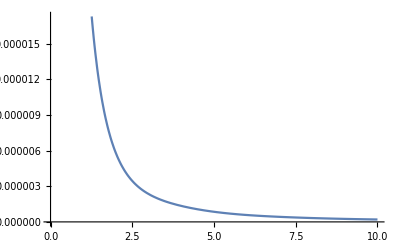

```mathematica
Plot[dPvcb/.{s-> 1, m-> 2,kp->0.1},{ko,0,10}]
```